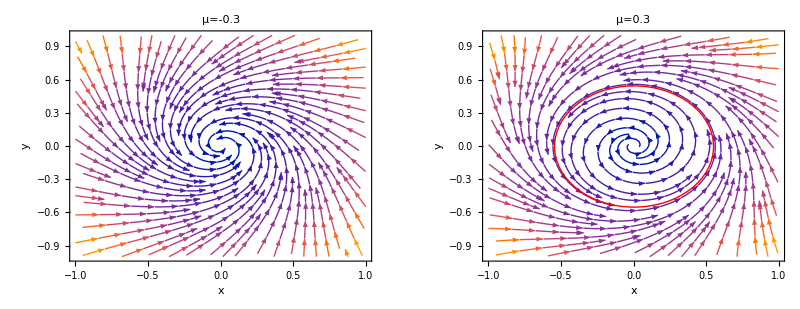

```mathematica
GraphicsRow[{With[{μ=-0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},AspectRatio->0.8,PlotLabel->"μ=-0.3",FrameLabel->{"x","y"}]],With[{μ=0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},Epilog->{Red,Circle[{0,0},√0.3]},AspectRatio->0.8,PlotLabel->"μ=0.3",FrameLabel->{"x","y"}]]}]
```

```mathematica
Series[(α r+ξ r^3+r^5 g1[ϕ])/(ω+η r^2+r^4 g2[ϕ]),{r,0,3}]
```

(α r)/ω+((-α η+ξ ω) r^3)/ω^2+O[r]^4

```mathematica
DSolve[{r'[ϕ]==(α r[ϕ])/ω,r[0]==r0},r[ϕ],ϕ]
```

{{r[ϕ]→ⅇ^((α ϕ)/ω) r0}}

```mathematica
DSolve[{u'[ϕ]==(α u[ϕ])/ω+(ⅇ^((α ϕ)/ω))^3(-α η+ξ ω)/ω^2,u[0]==0},u[ϕ],ϕ]//Simplify
```

{{u[ϕ]→-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)}}

```mathematica
Limit[-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω),α->0]
```

(ξ ϕ)/ω

```mathematica
-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)//Simplify
```

-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)

```mathematica
ClearAll["Global`*"];
(*f:向量场或映射 (List) x:自变量列表 (List) a:展开点 (List) k:多重线性型的阶数 (Integer)*)
MultilinearForm[f_,x_,a_,k_]:=Module[{tensorD},tensorD=D[f,{x,k}]/. Thread[x->a];
Function[Null,Block[{vecs={##}},Fold[Dot,tensorD,Reverse[vecs]]]]];
vars={x,y};
f={y,(α-x^2)y-x};
B=MultilinearForm[f,{x,y},{0,0},2];
CC=MultilinearForm[f,{x,y},{0,0},3];
Grad[f,{x,y}]/.{x->0,y->0}
Grad[f,{x,y}]/.{x->0,y->0}//Eigenvalues
Grad[f,{x,y}]/.{x->0,y->0}//Eigensystem
Transpose[Grad[f,{x,y}]]/.{x->0,y->0}//Eigensystem
```

{{0,1},{-1,α}}

{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))}

{{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))},{{1/2 (α+√(-4+α^2)),1},{1/2 (α-√(-4+α^2)),1}}}

{{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))},{{1/2 (-α-√(-4+α^2)),1},{1/2 (-α+√(-4+α^2)),1}}}

```mathematica
MyDot[x_,y_]:=Dot[Conjugate[x],y]
MySimplify[x_]:=Simplify[x,Assumptions->α∈Reals&&√(4-α^2)>0]
q={1/2 (α-I √(4-α^2)),1};
p={1/2 (-α-I √(4-α^2)),1}/(MyDot[q,{1/2 (-α-I √(4-α^2)),1}]//Expand//MySimplify);
MyDot[q,p]//Expand//MySimplify
```

1

```mathematica
ω=√(4-α^2);
g20=MyDot[p,B[q,q]]//MySimplify;
g11=MyDot[p,B[q,Conjugate[q]]]//MySimplify;
g21=MyDot[p,CC[q,q,Conjugate[q]]]//MySimplify;
1/(2 ω^2)Re[I g20 g11+ω g21]//MySimplify
```

-Re[(√(4-α^2) (2+α^2-ⅈ α √(4-α^2)))/(-4+α^2-ⅈ α √(4-α^2))]/(-4+α^2)

```mathematica
(√(4-α^2) (2+α^2-ⅈ α √(4-α^2))(-4+α^2+ⅈ α √(4-α^2)))/(16-4 α^2)//MySimplify
```

1/2 (3 ⅈ α-√(4-α^2))

```mathematica
(-4+α^2-ⅈ α √(4-α^2))(-4+α^2+ⅈ α √(4-α^2))//Expand
```

16-4 α^2